## Introduction

In December of 2023, a video was uploaded to YouTube by Scrabble Grandmaster (GM) Mack Meller. The video can be found at this link. Mack is the winner of the 2024 North American Scrabble Championship, and uploads videos almost every day of his games against the strongest Scrabble bots, or other GMs. 

I have played Scrabble with family ever since I can remember, and began playing online around 2 years ago. This video sparked a whole new interest in Scrabble for me.

## Terminology

I will start by defining some terminology, and I will assume that you know the basics of how to play Scrabble because you chose to read this post!

Bingo - A player uses all seven tiles on their rack in a single turn, receiving a 50-point bonus.
Blank - A blank tile can represent any letter, and scores zero points.
Overlap - A word is formed that uses a tile already on the board from a previous turn.
Hook - A word is played that places a letter onto the start or end of a word. For example: (S)TRAINER, TRAINER(S). The letter S has ‘hooked’ onto the word TRAINER.
Tile Bag - The distribution of exactly 100 tiles corresponding to letters in the English Alphabet or blanks. There are 9 As, 2 Bs, 2 Cs, 4 Ds, 12 Es, 2 Fs, 3 Gs, 2 Hs, 9 Is, 1 J, 1 K, 4 Ls, 2 Ms, 6 Ns, 8 Os, 2 Ps, 1 Q, 6 Rs, 4 Ss, 6 Ts, 4 Us, 2 Vs, 2 Ws, 1 X, 2 Ys, 1 Z, and 2 Blanks (usually represented by the “?” symbol).

## The Perfect Game

In the video, Mack takes us turn-by-turn through a fictional—but technically possible—Scrabble game between two players.
The game belongs to a specific set of all possible Scrabble games because of some interesting constraints:

Every turn, for both players, must be a bingo.

The game must end in a tie.

Note, there is also an implicit aim to score as many points as possible. I became fascinated by the difficulty in satisfying even the first of these constraints. 

So let’s see what a game like this would entail:
Player A goes first with a 7-letter bingo. 
Player B must play 7 letters too, either making use of an overlap through Player A’s turn to make an 8-letter word, or play a 7-letter word using an available hook. 
This continues back and forth, until each player has had seven turns—fourteen in total—and a total of 14 x 7 = 98 tiles exist on the Scrabble board.
Since Player B has the even-numbered turns, Player B has the final turn and Player A is left with two tiles (100 - 98 = 2). In competitive Scrabble, twice the total value of these two tiles is added to Player B’s final score.

## The Scrabble-gorithm

My goal was to algorithmically generate the fourteen valid bingos, using only the tiles available in the tile bag. My plan during this project was to define some checkpoints that constituted a successful ‘version’ of the problem:

Version 1: Generate fourteen 7-letter bingos, with no overlaps, using only the tiles available in the tile bag.

Version 2: Generate a starting 7-letter bingo followed by thirteen 8-letter bingos, each of which overlap a single tile from exactly one bingo that has already been played, and using only the tiles available in the Tile Bag.

Version 3: The same as version 2, but ensure the words fit on a standard 15x15 Scrabble board.

## Version 1: 7 Letter Bingos

Approaching this problem as a human, we almost have too clean a slate. Where do you even start? Perhaps you think of nine or ten bingos, making sure you avoid words like “ASSISTS” which blasts through 100% of your Ss. Inevitably, you reach a tile pool that looks bleak. You cannot seem to make out any possible 7-letter words, and perhaps even your precious vowel supply is running low, or too high!
I wanted to arrive at a solution faster than a human ever could. It is important to note that I did not start working on any visualizations on a “real” Scrabble Board until version 3. This challenge began as simply a computational word game.

My program has perfect word knowledge, thanks to a complete dictionary I imported.

```mathematica
dict = ;
wordsByLength = GroupBy[RandomSample[dict], StringLength];
```

I began by scrambling the dictionary randomly, and grouping the words according to their length. Remember we are only concerned with 7-letter words in this version. The crucial requirement of this algorithm is to keep track of the tiles you have remaining, so at the beginning of every iteration I defined remainingCounts to be an association of tile → quantity key-value pairs. You can see that this matches the tile bag I defined in the terminology.

```mathematica
tiles=;
remainingCounts=tiles[[All,"Quantity"]]
```

<|A→9,B→2,C→2,D→4,E→12,F→2,G→3,H→2,I→9,J→1,K→1,L→4,M→2,N→6,O→8,P→2,Q→1,R→6,S→4,T→6,U→4,V→2,W→2,X→1,Y→2,Z→1,?→2|>

I iterated through the scrambled list of 7-letter words and performed a check with each new word that it was constructable with the tiles specified in remainingCounts, ensuring this was updated after each constructable word. Unconstructable words that caused one or more values in remainingCounts to become negative were discarded, and the iteration continues until the list ends. For example, a word like “KINFOLK” would be refused from the jump due to their being only 1 K in the tile bag. 
The image below shows the algorithm in action for the first few bingos.

-Graphics-

The stochastic nature of this process sometimes leads one to a point where, even with 21 letters remaining, a valid 7-letter word cannot be constructed.

	-Graphics-

I can perform a check just to be sure.

```mathematica
CanFormWord[tiles_,word_]:=AllTrue[
  Tally[Characters[word]],
  (Count[Characters[tiles],#[[1]]]>=#[[2]])&
];
Select[wordsByLength[7],CanFormWord["AAAAEFFGGIIIIJOOQVVXY",#]&]
```

{}

But what about blanks? I hear you cry. Allowing for the use of a blank tile here would certainly enable many valid words to be played:

```mathematica
Table[Select[wordsByLength[7],CanFormWord[StringJoin["AAAAEFFGGIIIIJOOQVVXY",blank],#]&],{blank,ToUpperCase[Alphabet[]]}]//Flatten
```

{VIVIFIC,VAIVODE,AFFIXED,VOYAGED,VOIVODE,FOGGAGE,JIGAJIG,JIGAJOG,JEOFAIL,FOVEOLA,FOGGILY,FOLIAGE,AFFIXAL,LIXIVIA,GOOFILY,GEOLOGY,VILIAGO,IVYLEAF,EXOGAMY,MEGAFOG,VIFFING,GINGIVA,GOOFING,JAGAING,AFFYING,ANAGOGY,GOFFING,GEOGONY,YAFFING,JEFFING,VIVAING,VAGINAE,GAFFING,ANAGOGE,APAGOGE,RIFFAGE,FIGGERY,VOYAGER,OVERJOY,REAFFIX,FOGGIER,JAGGERY,FIGGIER,JAGGARY,FORGAVE,JIGGIER,FORGIVE,AGRAFFE,GARAGEY,AFFAIRE,AFFIXER,FOXFIRE,JAGGIER,GIRAFFE,VIVARIA,GOOFIER,AFFIXES,VOYAGES,FEIJOAS,GAVAGES,JAGGIES,JIFFIES,ISAGOGE,FOOTAGE,FIXATIF,QUAYAGE,WAVEOFF}

But in the example that ended with 23 tiles left, there are only 11 bingos in the “Bingos Found” list. There are still three turns left! Casual blank usage early on will almost certainly leave us stuck with nine letters on turn fourteen, out of which it would be impossible to make a bingo. 

This is where I make the decision to allow for the use of exactly one blank on turn thirteen, and exactly one blank on turn fourteen, giving us the degree of freedom when we need it most.
From a functionality perspective, this is as simple as allowing that exactly one key (letter) in remainingCounts may temporarily take on the value of -1 when remainingCounts is updated. This key (letter) is designated as the blank for that turn, then its value is set back to zero, and the value of the ? key within remainingCounts is decremented by one.

Here, we were only one bingo away from a successful iteration. By carefully examining the “Tiles Left”, one can see that the algorithm has employed a blank as a B to form the word PAXIUBA (a type of Brazilian palm tree) on turn thirteen. Unfortunately, even allowing the use of a blank on the final turn, there are no valid bingos that can be made from the remaining nine tiles.

-Graphics-

And so, all that is left is run this algorithm until we achieve fourteen bingos. 
I began uploading to a database in the Wolfram Cloud whenever I had a successful iteration, such that I can choose some cool examples to share. Furthermore, I kept track of the leftover tiles, and the letters employed as blanks.

-Graphics-

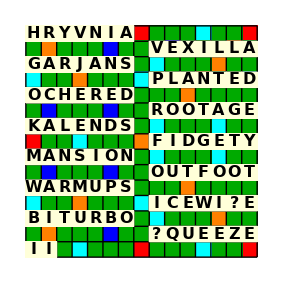
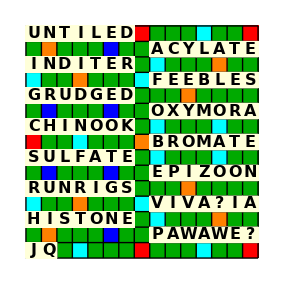
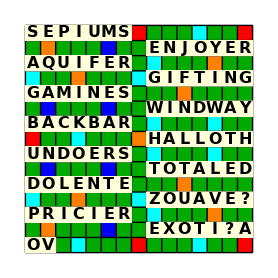
Here is a visualization on a Scrabble Board of some more examples. Bingos one to seven are on the left side from top to bottom, and bingos eight to fourteen are on the right. The two leftover tiles are in the lower left corner, and the blanks are indicated by question marks. 
 I find it fascinating to see which unusual bingos to which the algorithm has resorted for the later turns as a result of the strange mix of tiles remaining. Also, notice how the relative consonant/vowel-heaviness of the available pool of tiles in turns thirteen and fourteen affects the bingos that are selected.

Version 1 was complete.

-Graphics--Graphics-
-Graphics-

## Version 2: 8-Letter Bingos

Most of the hard work for this version had already been completed. I just needed a way of choosing the overlapping tile each turn. The overlapping tile must be a member of the intersection of characters in the new word, and characters in previous bingos.
The variable usedCounts is an association similar to remainingCounts, except it tracks the tiles used rather than the tiles remaining. In this example, it assumes the word SCIENCE was played first, and we are checking the overlap tile options for the word TUNGSTEN.

```mathematica
usedCounts=Sort[Counts[Characters["SCIENCE"]]];
word="TUNGSTEN";
overlapTileOptions=Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]
```

{E,N,S}

If this intersection is empty, the word is rejected and a new word is selected. 
The following is an example of that exact situation, which provokes a new selection of the bingo to be played in the second turn. It is worth mentioning that QUIZZIFY would also be rejected on the basis of having 2 Zs, however this check comes later. 
Perceptive readers might envisage the word QUIZZIFY perhaps being valid in turns thirteen or fourteen, provided that Z can be the overlap tile, and a blank is employed as the other Z. Fantastic!

-Graphics-

Also, the overlap tile must not be double-counted when updating the remaining tiles. In the example below, notice how there is only one S in the “Tiles Used” because I have accounted for the fact it is the overlap tile and would only appear once ‘on the board’.

-Graphics-

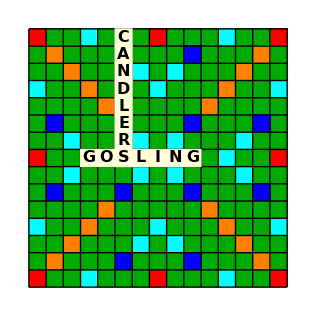

It is worth mentioning again that this visualization is merely to aid the reader’s understanding. Version 2 does not ‘care’ about board position—or actually being a valid Scrabble play. The only thing that matters is that we select words composed of tiles that remain within the constraints of the tile bag. 
What would this correspond to physically? I suppose it would mean that the Scrabble Board can be infinitely large, or perhaps that you are permitted to stack tiles on top of already played tiles (normal to the plane of the board).

So lets assume that we continue to add bingos to our catalogue, and we approach turns thirteen and fourteen. We are now at a stage where we must choose an overlap tile and we have the freedom to utilize a blank.  The algorithm first selects an overlap tile at random then determines the specific letter for the blank to represent, as in version 1. 
There may be instances where, for all possible tiles the blank could represent, the tile bag constraint is violated and a new bingo must be tried. 
Here is a snapshot from the end stages of version 2. One can see turns eleven, and twelve using overlap tiles only. On turn thirteen the algorithm reaches the word PROTOZOA; R is the chosen overlap tile and the word is deemed valid under the condition that the blank is employed as a P. 

-Graphics-

Notice the lack of any Ps or Rs in the “Tiles Left” after turn twelve; nor are there any more Ps or Rs in the “Tiles Used” after turn thirteen compared to the “Tiles Used” after turn twelve. 
Notice also the presence of one ? in the “Tiles Used”, and the “Tiles Left” after turn thirteen.

Again, we reach a point where all that is left is run this algorithm until we achieve fourteen bingos. 
I created a new database in the Wolfram Cloud which would be automatically updated whenever I had a successful iteration, this time making sure to keep track of the bingos, blanks, leftover tiles, and overlap tiles!

-Graphics-

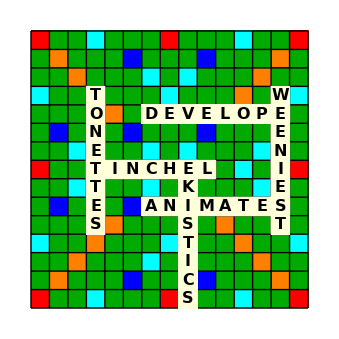
-Graphics-

This is a visualization of the first six turns in the game corresponding to one of the randomly sampled “successful” iterations. 
Upon writing this, I will say that this should be taken with a rather large pinch of salt. Board position not being taken into account makes it incredibly difficult to fit the words around one another while abiding by the given overlaps. I was quite lucky to have an example where I could show even six turns. 
Furthermore, a bug rears its head in the first entry of the dataset above, wherein the same O is chosen as the overlap tile for both turn two and three.

I hope to address these issues in version 3, by folding in board strategy with the algorithmic bingo generation.

## Version 3: Scrabble-gorithm

Hopefully versions 1 and 2 have satisfied those among you who enjoy word games. However, in version 3 we will explore if my method can be extended to resemble a feasible game of Scrabble.
It was at this point I needed some way to visualize the turns on a ‘real’ board, so I created some utility functions. 
The first—CreateInitialScrabbleBoard—uses the ArrayPlot function with some custom ColorRules to recreate a Graphics object in the style of an empty Scrabble board. It requires zero arguments.
The second—UpdateScrabbleBoard—employs a neat trick where it simply updates a list of graphics primitives representing tiles. This list can then be used as the Epilog for the result of CreateInitialScrabbleBoard[]. Therefore, successive uses of UpdateScrabbleBoard correspond to overlaying the tiles on a turn-by-turn basis, nicely concordant with how words are played in the real game. This function requires the word, the board position of the starting tile, the direction, and the current state of the Epilog as its arguments.
The rows of a Scrabble board are indexed from top to bottom by the letters A to O, and the columns are indexed from left to right by the numbers 1 to 15.

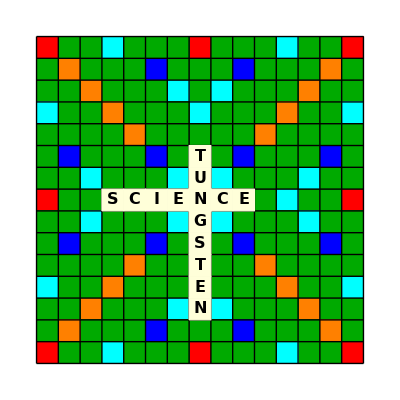

```mathematica
CreateInitialScrabbleBoard[]:=
Module[
{board,colors},board=;
colors={"TW"->Red,"SL"->Darker[Green],"DL"->Cyan,"TL"->Blue,"DW"->Orange};
ArrayPlot[board,ColorRules->colors,Mesh->True,MeshStyle->Black]
];
UpdateScrabbleBoard[word_,pos_List,direction_String:("Right"|"Down"),epilogState_]:=
Module[
{x,y,length,epilog},length=StringLength[word];
x=(pos[[2]]-1);
y=15-(LetterNumber[pos[[1]]]-1);
If[direction==="Right",
epilog=Table[{{LightYellow,EdgeForm[Thin],Rectangle[{x+(i-1),y},{x+i,y-1},RoundingRadius->0.2]},Text[Style[Characters[word][[i]],16,Bold],{x+(i-0.5),y-0.5}]},{i,length}],epilog=Table[{{LightYellow,EdgeForm[Thin],Rectangle[{x,y-(i-1)},{x+1,y-i},RoundingRadius->0.2]},Text[Style[Characters[word][[i]],16,Bold],{x+0.5,y-(i-0.5)}]},{i,length}]];
Join[epilogState,epilog]
];
board=CreateInitialScrabbleBoard[];
epilogState=UpdateScrabbleBoard["SCIENCE",{"H",4},"Right",{}];
epilogState=UpdateScrabbleBoard["TUNGSTEN",{"F",8},"Down",epilogState];
Show[board,Epilog->epilogState]
```

### Finding All Possible Overlap Plays

In the example above, I have simply picked a position at which to play the bingo TUNGSTEN such that it overlaps nicely with the starting bingo SCIENCE. However as I showed in version 2, the letters E, N, and S could have been the overlap tile. I needed a way to automate the generation of all options for where a new bingo can be played.

Assuming SCIENCE was played first as above, here are all of the potential positions for TUNGSTEN:

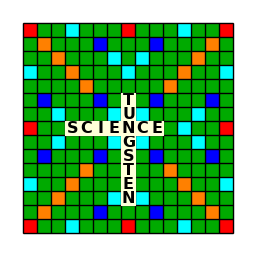
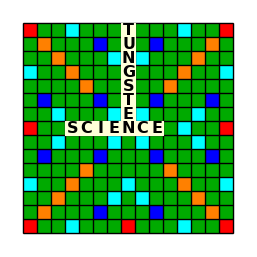
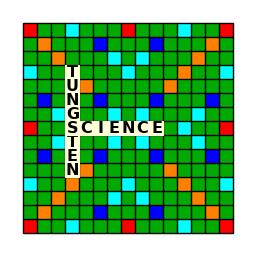
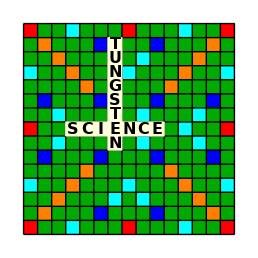
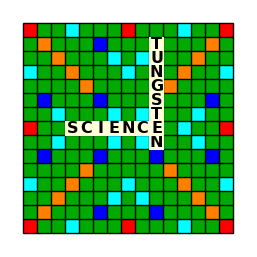

This is quite simple when there is only one word on the board with which we must overlap. Notably though, we must not look for plays that go horizontally through a word that has already been played horizontally. The requirement to store some more information about each bingo as it is played is now becoming clear. 

To handle this I decided to create an association for each turn that includes the bingo, the board position of the starting tile, the direction of play, and the tile to overlap. These were added to the master association representing the full iteration upon each new addition of a bingo. I coined the term overlap vector which was a list of elements that uniquely identified a new bingo in our game.

An initial naive approach of generating all of the possible positions to play a new bingo involved having far too many invalid options. Taking the leftmost arrangement of SCIENCE and TUNGSTEN, let us see what I mean by trying to place the word COMPUTER:

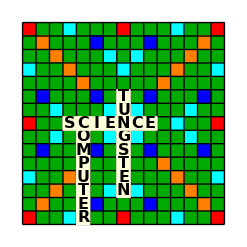
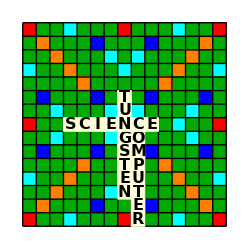
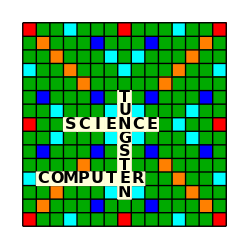
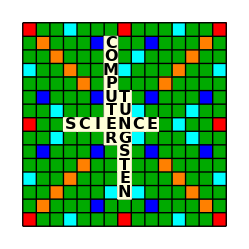
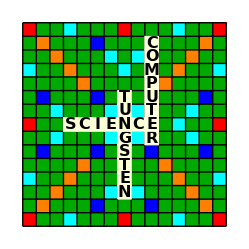
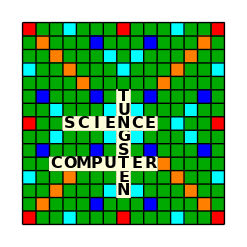
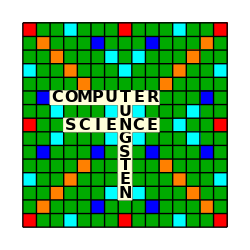
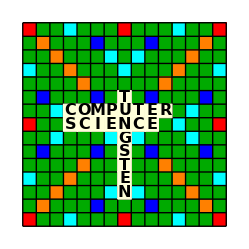

I have been deliberately exhaustive here to show that, while some of these options are valid plays, many are not. The naive approach allowed the algorithm to inadvertently find positions immediately adjacent to already played bingos. Avid Scrabble players will notice how sometimes this does in fact produce a valid 2-letter word! However we cannot rely on this, and I decided to make this kind of play illegitimate.
The logic to capture this extra constraint included the following steps:

For each new bingo position, define a seven or an eight-tile block that represents the board squares it will use up. I created a function called Battleship to achieve this. Hopefully the analogy is clear.

For each position, keep track of the existing bingo to be overlapped by the new one. Battleship was employed once again to define the seven or eight board squares it is using up.

For all other existing bingos that were not going to be overlapped by the new bingo, I defined a ‘forbidden zone’ around them. This ensured that no invalid plays would be found as a consequence of inadvertent overlaps with or hooks to other bingos. I achieved this with my ForbiddenSquares function. The graphic below shows in principle what is happening here. Given that the intended position for COMPUTER is through the E of TUNGSTEN, we want to avoid the ‘forbidden zone’ around SCIENCE.

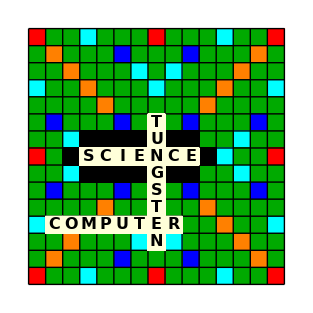

For each potential new bingo position we simply need to ensure that the intersection of the board squares between A. the Battleship defining the new bingo and B. the Battleship defining the existing bingo to be overlapped plus all ForbiddenSquares, is exactly one. This corresponds to a single tile overlap of the  new bingo with an existing bingo on the board.

My function FindPossibleOverlapPositions does all of this computation, and outputs a list of valid overlap vectors. This marked a huge step in the right direction, as we could now build up the catalogue of bingos with the confidence that they are all valid plays on a real Scrabble board.

### From Algorithm to Game

For each overlap vector, I could use my UpdateScrabbleBoard function to generate a potential Epilog.
At this point I grappled with the idea of making random choices of these overlap vectors, since each one was valid. However, after some experimenting, I concluded that random choices were simply not going to be careful enough about conserving board space—especially as the board fills up with more and more bingos. Therefore, I generated all possible arrangements and allowed the user to choose!
I used DynamicModule, Button functions for skipping and selecting a new bingo, and NotebookDelete[EvaluationCell[]] upon skipping or selecting to ensure that successive plays didn’t ‘pile up’ in the notebook. This was quite fortuitous as what started off as an algorithm had become a one-player game, so to speak, with a clear aim of squeezing fourteen valid bingos onto the board. 
Here is the game in action after the first few bingos:

-Graphics-

The above shows the state of the iteration when ORACLES, BRONCHIA, and SCULPTED have been selected, and we have been presented with all available positions in which we can play ANODIZER. The “Tiles Used” says 21 because until you ‘Select’ an option, the usedCounts and remainingCounts associations (yes, the same functionality as in version 1 and 2) only ‘know’ about the previous three turns.
It is worth pointing out that the same checks that a bingo is constructable with the available tiles in remainingCounts are being carried out here.

### Geometrically Feasible?

Things seemed to be going quite well, hence my panic when I considered the prospect of it actually being geometrically impossible to fit fourteen bingos on the board in this way. Recalling Mack Meller’s original video (as well as subsequent ones he has released), it makes heavy use of hooks, adjacent plays resulting in two-letter words, and nine-letter plays through disconnected bingos already on the board. These are useful tactics to conserve board space...and I am not allowing ANY of them! 
I set about trying to prove, by trial and error, that it is purely geometrically possible to do it my way.
A reminder of the (abstracted) geometric problem at hand:

You have a 15x15 Grid.

Start with a 7x1 rectangle that must go horizontally or vertically through the central square.

Stack thirteen additional 8x1 rectangles, one at a time, vertically or horizontally, on the grid. You must stack such that each new rectangle overlaps with the current rectangles at exactly 1 square.

Thankfully, it did not take too long to find a valid solution. I created some custom functions to be used alongside the existing UpdateScrabbleBoard function to help visualize the process.  The graphic below shows the first solution that I found, with each bingo numbered and its direction indicated.

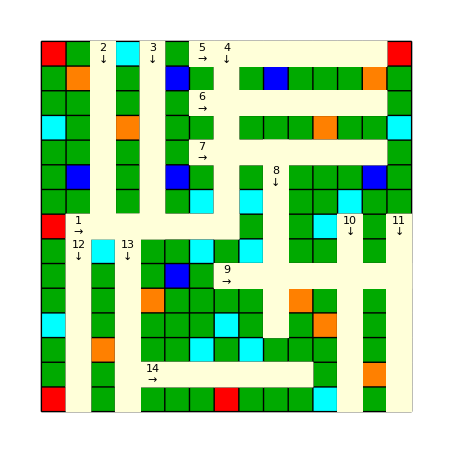

This shows how strategic one must be to successfully finish the iteration. Despite there being only 98 tiles to place and 15 x 15 = 225 squares in which to place them, the constraints I explained relating to ‘forbidden zones’ make this a non-trivial feat. 
I would like to leave something as an exercise to the reader: How many unique board arrangements are there? Clearly the one animated above is not the only one, but how many more? Surely a finite number? 
After this brief digression, I could return to the problem at hand which is placing actual words on the board!

### Nearing The Endgame

Now I had a framework to follow when faced with the option to ‘Skip’ or ‘Select’ any given bingo. I was required to be patient and wait until I arrived at a bingo that made efficient use of available board space, if I wanted to get past the nine or ten bingo mark. 
In the example below, because the ‘Skip’ button grants me more freedom to choose, I have also taken care to include common words. Admittedly, the dictionary I am using (Collins Scrabble Word List 2021) contains many words with which I am unfamiliar.

-Graphics-
-Graphics-

We are seeing the state of the board after eleven valid bingos, and it is showing us that it has found one possible place to play the twelfth bingo of BADMOUTH. 
Notice how I have included a tracker which tells us when we have exhausted each quarter of the ~40,000 eight-letter words in the dictionary. 
After turn eleven it had only reached position 1671 in the list, whereas by turn twelve it had checked over 30,000 words! This does not mean I pressed ‘Skip’ ~29,000 times. The overwhelming majority of bingos are discounted automatically due to being unconstructable with the tiles remaining, or constructable but there is nowhere for them to go. You only have to ‘Skip’ when there is a valid play and you do not like it.

Underneath the board, I have included the “Tiles Used” and “Tiles Left” after BADMOUTH was selected.
Some quick scanning of remaining board space shows us that there is actually only one position in which we can play another bingo: down through the first W of DOWNWASH. Looks like we are getting at most thirteen bingos here. If the algorithm had found a play down to the M in MIRAGES, it would have kept alive the 3rd column down from the I in MIRAGES—but no luck.

### Using Blanks

Even though (in the above iteration) attempts to find fourteen bingos are futile, it raises a good opportunity to discuss the usage of blanks. 
Taking our remaining tiles, the W in DOWNWASH, and allowing the use of one blank, we have a number of options for our thirteenth bingo.

```mathematica
constructableWords=Table[Select[wordsByLength[8],CanFormWord[StringJoin["DEFFIJOOTUUXYY","W",blank],#]&],{blank,ToUpperCase[Alphabet[]]}]//Flatten;
playableWords=Select[constructableWords,StringPart[#,1]=="W"||StringPart[#,2]=="W"&] (* W must be the first or second letter, see board. *)
```

{WIFEHOOD,WOODRUFF,WRITEOFF,WOODIEST,WOOFIEST,WIDEOUTS}

Looking to a new iteration, I have reached the point where it is finding potential plays for turn thirteen. 
The algorithm has found the words ALTITUDE (which I skipped) and SMOOTHIE. The latter is displayed on the board with a styled blank tile in place of the M.

-Graphics-

After a few more ‘Skips’, we reach the word SAWTOOTH. Interestingly, we have two valid places to play this bingo: down through the T of KIBIBYTE with a blank S, or right from the S of GROOVERS...without needing a blank. Yes, the algorithm can find instances where you could play the same bingo in two different places, one needing a blank and one not!

-Graphics-

Naturally, one might choose the option where you do not need to use a blank. And thankfully I have written some functionality into the algorithm such that, if no blanks were used on turn thirteen, one has two blanks to use on turn fourteen.
On turn thirteen, if we played SAWTOOTH through the T of KIBIBYTE, we would have the following tiles left: DEEITUUZ?. Also, we would be forced to play from the S of GROOVERS.
Playing SAWTOOTH from the S in GROOVERS, we would have the following tiles left: DEEIUUZ??. Also, we would be free to play through the Y, T, or E of KIBIBYTE. This leaves us with much more freedom, and hopefully, many more valid bingos from which to choose.
Below, I have included just a small sample of valid options for turn fourteen. 
Note the lack of need for both blanks when playing DEPUTIZE, leaving U? as the remaining two tiles. Note also the two positions in which QUIETUDE can be played.

-Graphics-

-Graphics--Graphics-
-Graphics-
-Graphics-

Version 3, and the Scrabble-gorithm was complete!

## Summary

I am very happy with how this project turned out, and the ease with which one can go from idea to interactive visualization using Wolfram Language was a great help throughout. I have again kept a database of ‘Perfect Games’ that result from a successful iteration. 
Included with this post is a self-contained notebook which will allow you to have a go at this yourself, and I welcome any feedback on the code (josephb@wolfram.com). I am particularly interested in having it run in the Wolfram Cloud, enabling me to crowd-source data. Also, an obvious next step would be finding out how many points are scored, but alas, I wanted to share this as soon as I had unlocked the capability of generating perfect games. 
Finally, the image below shows one of the first ever ‘perfect games’ I was able to algorithmically generate. Demonstrably, including common words was not a priority! 
Here are some favourites:

LOGJUICE - poor quality port wine

DIATRETA - a type of decorative Roman bowl or cup made of glass

ORATORIO - a long piece of music with a religious theme which is written for singers and an orchestra

OOZINESS - the quality or state of being muddy or slimy

VOLVOXES - (plural) any freshwater flagellate protozoan of the genus Volvox, occurring in colonies in the form of hollow multicellular spheres

QUEENDOM - a territory, state, people, or community ruled over by a queen.

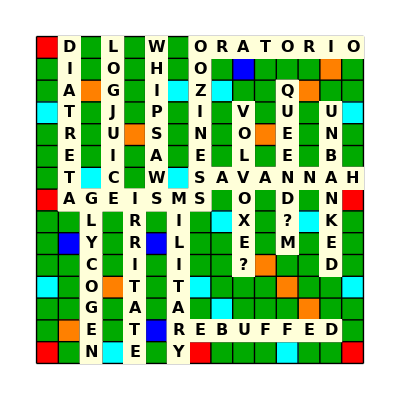

Thank you for reading.

```mathematica
Button[Style["Run Initialization",20,FontFamily->"Arial"],FrontEndExecute[FrontEndToken["EvaluateInitialization"]],Evaluator->Automatic]
```

Run Initialization

```mathematica
RunScrabblegorithm[]
```

## Initialization

```mathematica
tiles=;

(* Updates association containing (Tile -> No. Used) pairs. *)
UpdateUsedTileCount[usedCounts_,word_]:=
Module[
{charCounts},charCounts=Counts[Characters[word]];
Merge[{usedCounts,charCounts},Total]
]

(* Updates association containing (Tile -> No. Remaining) pairs. *)
UpdateRemainingTileCount[remainingCounts_,word_,blanks_]:=
Module[
{tiles=Characters[word],charCounts,newCounts,blanksNeeded},
charCounts=Counts[Characters[word]];
newCounts=Merge[{remainingCounts,Map[(#->(remainingCounts[#]-charCounts[#]))&,tiles]},Last];
blanksNeeded=Abs[Total[Select[Values[newCounts],#<0&]]];
If[blanksNeeded<=blanks&&Min[Values[newCounts]]>=-blanks,newCounts["?"]=newCounts["?"]-blanksNeeded;
Return[newCounts],Return[remainingCounts]
]
]

(* Create Graphic of an Empty Scrabble Board. *)
CreateInitialScrabbleBoard[]:=
Module[{board,colors},
board=;
colors={"TW"->Red,"SL"->Darker[Green],"DL"->Cyan,"TL"->Blue,"DW"->Orange};
ArrayPlot[board,ColorRules->colors,Mesh->True,MeshStyle->Black]
]

(* Create the Epilog of a 'word' played in a position 'pos' in the following 'direction'. *)
UpdateScrabbleBoard[word_,pos_List,direction_String:("Right"|"Down"),epilogState_]:=
Module[{x,y,length,epilog},
length=StringLength[word];
x=(pos[[2]]-1);
y=15-(LetterNumber[pos[[1]]]-1);
If[direction==="Right",
epilog=Table[{{LightYellow,EdgeForm[Thin],Rectangle[{x+(i-1),y},{x+i,y-1},RoundingRadius->0.2]},Text[Style[Characters[word][[i]],16,Bold],{x+(i-0.5),y-0.5}]},{i,length}],epilog=Table[{{LightYellow,EdgeForm[Thin],Rectangle[{x,y-(i-1)},{x+1,y-i},RoundingRadius->0.2]},Text[Style[Characters[word][[i]],16,Bold],{x+0.5,y-(i-0.5)}]},{i,length}]
];
Join[epilogState,epilog]
]

(* Finds list of possible starting positions of a new bingo. *)FindStartingSquares[boardRow_Integer,boardCol_Integer,retrace_,toTile_,dirOfPlay_]:=Module[{posList},If[dirOfPlay=="Down",posList={ToUpperCase[FromLetterNumber[boardRow-retrace]],boardCol+toTile};
Flatten[Outer[List,posList[[1]],posList[[2]]],1],posList={ToUpperCase[FromLetterNumber[boardRow+toTile]],boardCol-retrace};
Flatten[Outer[List,posList[[1]],posList[[2]]],1]]]

(* Takes the current Master Association, the word to be played, and the possible options for the overlap tile,and finds an association in the form:<|"Down" -> <|"OverlapTileOption" -> {pos1,pos2,...}|>, "Right" -> <|...|>|>. Then returns a list of valid 'overlap vectors' subject to board constraints.
*)
FindPossibleOverlapPositions[assoc_,word_,overlapTileOptions_List]:=
Module[{overlapAssoc=<|"Down"-><||>,"Right"-><||>|>,overlapVectors,overlapSquaresAssoc},
Map[(* Map over overlap tiles. *)
Function[{tile},
Map[(* Map over played bingos. *)
Function[{i},
Module[{direction,boardRow,boardCol,bingo=assoc[[i]]["Bingo"],toTile,retrace,avoidCols,posListDown,filterPosListDown,avoidRows,posListRight,filterPosListRight},
direction=assoc[[i]]["Direction"];(* Find direction of played bingo. *)
{boardRow,boardCol}=assoc[[i]]["Position"];(* Find position of played bingo. *)
boardRow=LetterNumber[boardRow];
toTile=StringPosition[assoc[[i]]["Bingo"],tile][[All,1]]-1;(* Find position of overlap tile within played bingo. *)
retrace=StringPosition[word,tile][[All,1]]-1;(* Find position of overlap tile within new bingo. *)

(* Play "Down" through this already-played word, as it is directed to the "Right". *)
If[direction=="Right",
avoidCols=Values[Select[assoc,#["Direction"]=="Down"&][[All,"Position"]]][[All,2]];(* Do not play "Down" through existing "Down" bingos. *)
posListDown=FindStartingSquares[boardRow,boardCol,retrace,toTile,"Down"];
filterPosListDown=Select[posListDown,FreeQ[avoidCols,#[[2]]]&&LetterNumber[#[[1]]]<=8&&LetterNumber[#[[1]]]>=1&];
If[filterPosListDown=!={},If[!KeyExistsQ[overlapAssoc["Down"],tile],overlapAssoc["Down"][tile]=<||>];
If[!KeyExistsQ[overlapAssoc["Down"][tile],bingo],overlapAssoc["Down"][tile][bingo]={}]
];
If[filterPosListDown=!={}&&KeyExistsQ[overlapAssoc["Down"][tile],bingo],overlapAssoc["Down"][tile][bingo]=Join[overlapAssoc["Down"][tile][bingo],filterPosListDown]
],(* Update overlapAssoc. *)

(* Else, play "Right" through this already-played word, as it is directed "Down". *)
avoidRows=Values[Select[assoc,#["Direction"]=="Right"&][[All,"Position"]]][[All,1]];(* Do not play "Right" through existing "Right" bingos.*)
posListRight=FindStartingSquares[boardRow,boardCol,retrace,toTile,"Right"];
filterPosListRight=Select[posListRight,FreeQ[avoidRows,#[[1]]]&&#[[2]]>0&&#[[2]]<=8&];
If[filterPosListRight=!={},If[!KeyExistsQ[overlapAssoc["Right"],tile],overlapAssoc["Right"][tile]=<||>];
If[!KeyExistsQ[overlapAssoc["Right"][tile],bingo],overlapAssoc["Right"][tile][bingo]={}]
];
If[filterPosListRight=!={}&&KeyExistsQ[overlapAssoc["Right"][tile],bingo],overlapAssoc["Right"][tile][bingo]=Join[overlapAssoc["Right"][tile][bingo],filterPosListRight]
]
]
]
],Range[Length[assoc]]
]
],overlapTileOptions
];
overlapAssoc=Select[overlapAssoc,#=!=<||>&];(* After turn 1 there will be no "Right" overlaps. *)overlapVectors=Flatten[Table[{#,dir,tile,bingo}&/@overlapAssoc[dir][tile][bingo],{dir,Keys[overlapAssoc]},{tile,Keys[overlapAssoc[dir]]},{bingo,Keys[overlapAssoc[dir,tile]]}],3];(* Obtain all combinations of position, direction, and tile.*)
(*For each vector, where is it overlapping with 'forbidden' squares? *)
overlapSquaresAssoc=Map[#->Intersection[Battleship[word,#[[1]],#[[2]]],UpdateForbiddenSquares[assoc,#[[4]]]]&,overlapVectors];
Keys[Select[overlapSquaresAssoc,Length[Values[#]]==1&]] (* Select overlap vectors that overlap exactly one square. *)
]

(* Identify squares used up by a 'word' placed at 'startPos'. *)
Battleship[word_,startPos_,direction_]:=
Module[{row,col,length=StringLength[word]},
{row,col}=startPos;
If[direction==="Right",Table[{row,col+i},{i,0,length-1}],Table[{ToUpperCase[FromLetterNumber[LetterNumber[row]+i]],col},{i,0,length-1}]]
]


(* Identify squares in the 'forbidden zones' around already played words. *)
ForbiddenSquares[word_,startPos_,direction_]:=
Module[{row,col,length=StringLength[word],mainPositions,abovePositions,belowPositions,leftPositions,rightPositions},
{row,col}=startPos;
If[direction==="Right",mainPositions=Table[{row,col+i},{i,-1,length}];
abovePositions=Table[{ToUpperCase[FromLetterNumber[LetterNumber[row]-1]],col+i},{i,0,length-1}];
belowPositions=Table[{ToUpperCase[FromLetterNumber[LetterNumber[row]+1]],col+i},{i,0,length-1}];
Join[mainPositions,abovePositions,belowPositions],
mainPositions=Table[{ToUpperCase[FromLetterNumber[LetterNumber[row]+i]],col},{i,-1,length}];
leftPositions=Table[{ToUpperCase[FromLetterNumber[LetterNumber[row]+i]],col-1},{i,0,length-1}];
rightPositions=Table[{ToUpperCase[FromLetterNumber[LetterNumber[row]+i]],col+1},{i,0,length-1}];
Join[mainPositions,leftPositions,rightPositions]
]
]

(* Update 'forbidden squares taking into account the bingo to be overlapped. *)
UpdateForbiddenSquares[assoc_,bingo_]:=
DeleteDuplicates[
Flatten[
Values[
Map[
With[{word=#["Bingo"],pos=#["Position"],dir=#["Direction"]},
If[word==bingo,Battleship[word,pos,dir],ForbiddenSquares[word,pos,dir]]
]&,assoc
]
],1
]
]

(* Uses 'blankAssoc' to retrieve the blank(s) required for this play. *)
IdentifyBlanks[overlapVector_,blankAssoc_]:=SelectFirst[blankAssoc,#["Overlap"]==overlapVector[[3]]&]["Blank"]

(* Formats word to be displayed with its blanks as "?" tiles. *)
FormatWordWithBlanks[word_,blanks_]:=
Module[{formatWord=word},
Map[
Module[{blankIndices=StringPosition[word,#][[All,1]]},
If[Length[blankIndices]>Count[blanks,#],blankIndices={RandomChoice[blankIndices]}];
formatWord=StringReplacePart[formatWord,ToLowerCase[#],{#,#}&/@blankIndices]
]&,blanks
];
Return[formatWord]
]

(* Determines the blanks allowed at this stage of the game. *)
BlanksAllowed[assoc_,usedCounts_]:=
Module[
{blanksUsed=usedCounts["?"],b},
If[Length[assoc]<12,b=0,If[Length[assoc]==13&&blanksUsed==0,b=2,b=1]
];
Return[b]
]

RunScrabblegorithm[]:=
Module[
{wordsByLength=GroupBy[RandomSample[],StringLength],board=CreateInitialScrabbleBoard[],assoc=<||>},
i=1;
While[Length[assoc]<14,(* Turn 1. *)
While[Length[assoc]==0,
remainingCounts=tiles[[All,"Quantity"]];(* Whole tile bag remaining. *)
usedCounts=AssociationThread[Keys[tiles],Table[0,27]];(* Initially zero tiles have been used. *)
b=BlanksAllowed[assoc,usedCounts];
Module[{next=False},
pos={"H",2};
word=wordsByLength[7][[i]];
If[UpdateRemainingTileCount[remainingCounts,word,b]===tiles[[All,"Quantity"]],(* Starting 7-letter word must not require blanks. *)Print[word,": Choose another Starter"];
next=True
];
Module[{boardTurn1},
boardTurn1=
Row[{
DynamicModule[
{currentBoard=board,localEpilogState},
localEpilogState=UpdateScrabbleBoard[word,pos,"Right",{}];
Column[{
Show[currentBoard,ImageSize->300,Epilog->localEpilogState],
Button["Select",
AppendTo[assoc,1-><|"Bingo"->word,"Position"->pos,"Direction"->"Right"|>];
remainingCounts=UpdateRemainingTileCount[remainingCounts,word,b];
usedCounts=UpdateUsedTileCount[usedCounts,word];
epilogState=localEpilogState;
next=True;(* Flag is set to True when word is selected. *)
Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
NotebookDelete[EvaluationCell[]];
]
}]
],
Button["Skip",next=True;NotebookDelete[EvaluationCell[]]]
}];
If[next==False,Print[boardTurn1]];
WaitUntil[next===True];
next=False;
];
];
i++;
If[i>Length[wordsByLength[7]],Abort[]];
If[Length[assoc]==1,i=1]];
(* Turns 2-12. *)
While[1<=Length[assoc]<12,
Module[{next=False},(* Initialize flag. *)
word=wordsByLength[8][[i]];
overlapTileOptions=Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]];
If[overlapTileOptions==={},Print[word," Has No Overlaps!"];next=True];
b=BlanksAllowed[assoc,usedCounts];
Map[(* Check the remaining counts for each overlap option. *)If[UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b]==remainingCounts,overlapTileOptions=DeleteCases[overlapTileOptions,#] 
]&,overlapTileOptions
];
If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
If[overlapVectors==={},next=True];
possibleEpilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,overlapVectors];
Module[
{boardOptions},
boardOptions=
Row[
Join[
Table[
DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
Button["Select",
AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
remainingCounts=UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],b];
usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
epilogState=localEpilogState;
next=True;(* Flag is set to True when word is selected. *)
Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
Print["Bingos Checked: ",i];
NotebookDelete[EvaluationCell[]]
]
}]
],{idx,Length[overlapVectors]}
],
{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
]
];
i++;
If[i==10000,Print["25% Bingos Checked"]];
If[i==20000,Print["50% Bingos Checked"]];
If[i==30000,Print["75% Bingos Checked"]];
If[i>Length[wordsByLength[8]],Print["Sorry! Try Again!"]; Abort[]];
If[Length[assoc]==12,i=1]
];
(* Turns 13 and 14. *)
Module[{next=False},(* Initialize flag. *)
word=wordsByLength[8][[i]];
overlapTileOptions=Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]];
If[overlapTileOptions==={},Print[word," Has No Overlaps!"];next=True];
b=BlanksAllowed[assoc,usedCounts];
blankAssoc={};
(* Identify blanks and update 'blankAssoc'. *)
Map[
Module[
{newRemainingCounts,negativeKeys},
newRemainingCounts=UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b];
If[newRemainingCounts==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#],
negativeKeys=Flatten[Table[#,{-newRemainingCounts[#]}]&/@Select[Keys[newRemainingCounts],newRemainingCounts[#]<0&]];
If[negativeKeys=!={},
AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->negativeKeys|>],
AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->Null|>]
]
]
]&,overlapTileOptions
];
If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
If[overlapVectors==={},next=True,Echo@word;
{overlapVectors,possibleEpilogs}=
Module[{vectors,epilogs,blankVectors,wordOptions,blankEpilogs},
vectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]==Null&];
epilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,vectors];
blankVectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]=!=Null&];
blankVectors=Map[Append[#,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
wordOptions=AssociationMap[FormatWordWithBlanks[word,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
blankEpilogs=AssociationMap[UpdateScrabbleBoard[StringReplace[wordOptions[#],c_/;LowerCaseQ[c]:>"?"],#[[1]],#[[2]],epilogState]&,blankVectors];
{Join[vectors,blankVectors],Join[epilogs,blankEpilogs]}
]
];
Module[
{boardOptions},
boardOptions=
Row[
Join[
Table[
DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
Button["Select",i=1;
AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
If[Length[overlapVectors[[dIdx]]]==5,
usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->Flatten[{overlapVectors[[dIdx]][[3]],overlapVectors[[dIdx]][[5]]}]]]];
remainingCounts=UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],Length[overlapVectors[[dIdx]][[5]]]];
Map[remainingCounts[#]++&,overlapVectors[[dIdx]][[5]]];
usedCounts["?"]=usedCounts["?"]+Length[overlapVectors[[dIdx]][[5]]],
usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
remainingCounts=UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],0]
];
epilogState=localEpilogState;
next=True;
Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
 If[Length[assoc]<14,NotebookDelete[EvaluationCell[]]]
]
}]
],{idx,Length[overlapVectors]}
],{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
];
];
i++;
If[i==10000,Print["25% Bingos Checked"]];
If[i==20000,Print["50% Bingos Checked"]];
If[i==30000,Print["75% Bingos Checked"]];
If[i>Length[wordsByLength[8]],Print["Sorry! Try Again!"];Abort[]];
If[Length[assoc]==14,
Print["Congratulations!"];
Print[Dataset[assoc]];
obj=CloudGet["PerfectScrabbleGames"];
CloudPut[AppendTo[obj,assoc],CloudObject[["https://www.wolframcloud.com/obj/josephb/PerfectScrabbleGames"](https://www.wolframcloud.com/obj/josephb/PerfectScrabbleGames)]]
]
]
]
```

## CITE THIS NOTEBOOK

Generating the perfect Scrabble game
by Joseph Brennan
Wolfram Community, STAFF PICKS, December 16, 2024
https://community.wolfram.com/groups/-/m/t/3339808